```mathematica
f[p_,M_,T_]:=1/(E^((√(p^2+M^2))/T)+1);
fBol[p_,M_,T_]:=((2π)/(M T))^(3/2)E^(-(p^2/(2M))/T);
fRel[p_,M_,T_]:=f[p,0,T];
```

```mathematica
compare[M_,fun_]:=LogLogPlot[Evaluate[{
NIntegrate[1/(2 π^2)fun[p,M]f[p,M,T] p^2,{p,0,∞}]/NIntegrate[1/(2 π^2)f[p,M,T] p^2,{p,0,∞}],
NIntegrate[1/(2 π^2)fun[p,0]fRel[p,M,T] p^2,{p,0,∞}]/NIntegrate[1/(2 π^2)fRel[p,M,T] p^2,{p,0,∞}],
(((2π)/(M T))^(3/2)E^(M/T)NIntegrate[1/(2 π^2)fun[p,M]fBol[p,M,T] p^2,{p,0,∞}])/(((2π)/(M T))^(3/2)E^(M/T)NIntegrate[1/(2 π^2)fBol[p,M,T] p^2,{p,0,∞}])
}/(NIntegrate[1/(2 π^2)fun[p,M]f[p,M,T] p^2,{p,0,∞}]/NIntegrate[1/(2 π^2)f[p,M,T] p^2,{p,0,∞}])],{T,M/100,M*5},PlotRange->{All,{0.5,1}}];
```

NIntegrate::inumr: The integrand (p^2 √(90000+p^2))/(2 (1+ⅇ^((√(90000+Power[«2»]))/T)) π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand p^2/(2 (1+ⅇ^((√(90000+Power[«2»]))/T)) π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand ((p^2)^(3/2))/(2 (1+ⅇ^((√(p^2))/T)) π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

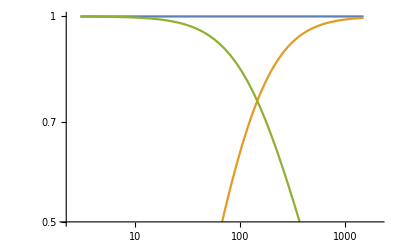

```mathematica
Energy[p_,M_]:=√(p^2+M^2);
compare[300,Energy]
```

NIntegrate::inumr: The integrand p^3/(2 (1+ⅇ^((√(90000+Power[«2»]))/T)) π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand p^2/(2 (1+ⅇ^((√(90000+Power[«2»]))/T)) π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand p^3/(2 (1+ⅇ^((√(p^2))/T)) π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

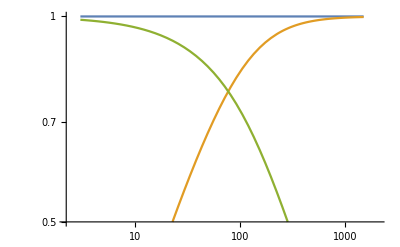

```mathematica
Momentum[p_,M_]:=p;
compare[300,Momentum]
```